```mathematica
SetDirectory["/Users/marco/marco.live/DIDATTICA/CORSI/2023-2024/IN450/esoneri/ESO1"];
Get["/Users/marco/marco.live/DIDATTICA/CORSI/2023-2024/IN450/code/cryptolib.ma"]
testo=StringDrop[Import["testo.txt"],146];

CoincidenceIndex[testo]
plaintext=TextCode[testo];
Plus@@(Map[First,DistributionA[plaintext]]^2)
```

```mathematica
ita=Import["http://www.corriere.it"];
divina="nelmezzodelcammindinostravitamiritrovaiperunaselvaoscuracheladirittaviaerasmarritaahiquantoadirqualeraecosaduraestaselvaselvaggiaeaspraefortechenelpensierrinovalapauratanteamarachepocoepiumortemapertrattardelbenchivitrovaidirodelaltrecosechivhoscorteiononsobenridircomivintraitanterapiendisonnoaquelpuntochelaveraceviaabbandonaimapoichifuialpieduncollegiuntoladoveterminavaquellavallechemaveadipaurailcorcompuntoguardaiinaltoevidilesuespallevestitegiaderaggidelpianetachemenadrittoaltruiperognecalleallorfulapauraunpocoquetachenellagodelcormeraduratalanottechipassaicontantapietaecomequeicheconlenaaffannatauscitofuordelpelagoalarivasivolgealacquaperigliosaeguatacosilanimomiochancorfuggivasivolsearetroarimirarlopassochenonlasciogiamaipersonavivapoicheiposatounpocoilcorpolassoripresiviaperlapiaggiadisertasichelpiefermosempreeralpiubassoedeccoquasialcominciardelertaunalonzaleggieraeprestamoltochedipelmacolatoeracovertaenonmisipartiadinanzialvoltoanzimpedivatantoilmiocamminochifuiperritornarpiuvoltevoltotemperadalprincipiodelmattinoelsolmontavansuconquellestellecheranconluiquandolamordivinomossediprimaquellecosebellesichabenesperarmeracagionediquellafieraalagaettapelleloradeltempoeladolcestagionemanonsichepauranonmidesselavistachemapparvedunleonequestipareachecontramevenisseconlatestaltaeconrabbiosafamesichepareachelaerenetremesseedunalupachedituttebramesembiavacarcanelasuamagrezzaemoltegentifegiavivergramequestamiporsetantodigravezzaconlapaurachusciadisuavistachioperdeilasperanzadelaltezzaequalequeichevolontieriacquistaegiugneltempocheperderlofacechentuttisuoipensierpiangeesattristatalmifecelabestiasanzapacechevenendomincontroapocoapocomiripignevaladovelsoltacementrechirovinavainbassolocodinanzialiocchimisifuoffertochiperlungosilenziopareafiocoquandovidicostuinelgrandisertomisereredimegridaialuiqualchetusiiodombraodomocertorispuoseminonomoomogiafuieliparentimieifuronlombardimantoaniperpatriaambeduinacquisubiulioancorchefossetardievissiaromasottolbuonoaugustoneltempodelideifalsiebugiardipoetafuiecantaidiquelgiustofigliuoldanchisechevenneditroiapoichelsuperboilionfucombustomatupercheritorniatantanoiaperchenonsaliildilettosomontecheprincipioecagiondituttagioiaorsetuquelvirgilioequellafontechespandidiparlarsilargofiumerispuosioluiconvergognosafronteodelialtripoetionoreelumevagliamillungostudioelgrandeamorechemhafattocercarlotuovolumetuselomiomaestroelmioautoretusesolocoluidacuiotolsilobellostilochemhafattoonorevedilabestiapercuiomivolsiaiutamidaleifamososaggiochellamifatremarleveneeipolsiateconvientenerealtroviaggiorispuosepoichelagrimarmividesevuocampardestolocoselvaggiochequestabestiaperlaqualtugridenonlasciaaltruipassarperlasuaviamatantolompediscecheluccideehanaturasimalvagiaeriachemainonempielabramosavogliaedopolpastohapiufamechepriamoltisonlianimaliacuisammogliaepiusarannoancorainfinchelveltroverrachelafaramorircondogliaquestinonciberaterranepeltromasapienzaamoreevirtuteesuanazionsaratrafeltroefeltrodiquellaumileitaliafiasalutepercuimorilaverginecammillaeurialoeturnoenisodiferutequestilacacceraperognevillafinchelavrarimessanelonfernolaondenvidiaprimadipartillaondioperlotuomepensoediscernochetumiseguieiosarotuaguidaetrarrottidiquiperlocoetternooveudirailedisperatestridavedrailiantichispiritidolentichalasecondamorteciascungridaevederaicolorchesoncontentinelfocoperchesperandivenirequandochesiaalebeategentialequaipoisetuvorraisalireanimafiaaciopiudimedegnaconleitilasceronelmiopartirechequelloimperadorchelasuregnaperchifuribellantealasualeggenonvuolchensuacittapermesivegnaintuttepartiimperaequivireggequivielasuacittaelaltoseggioohfelicecoluicuivieleggeeioaluipoetaiotiricheggioperquellodiochetunonconoscestiaciochiofuggaquestomaleepeggiochetumimeniladovordicestisichioveggialaportadisanpietroecolorcuitufaicotantomestiallorsimosseeiolitennidietro";

(* uso la distribuzione del testo per autocorrelare la parte estratta nel cifrato*)

refita=TextCode@divina;
mita=CoincidenceIndex[refita]
DistributionA[refita]


refita=plaintext;
mita=CoincidenceIndex[refita]
DistributionA[refita]
```

```mathematica
key=TextCode["spada"]
Print["Statistical Characteristics of plaintext blocks :"];
Map[DistributionA,blocks=Transpose@Partition[plaintext,m]]
ciphertext=Flatten@Transpose@Mod[blocks+key,26];FromCode@ciphertext
```

```mathematica
m=Length@key

Print["Statistical Characteristics of plaintext blocks :"];
Map[DistributionA,blocks=Transpose@Partition[plaintext,m]]

CoincidenceIndex[refita]
CoincidenceIndex[plaintext]

Print["Statistical Characteristics of ciphertext blocks :"];
MutualInformation[ciphertext,refita]
Map[CoincidenceIndex,blocks=Transpose@Partition[ciphertext,m]]

Map[DistributionA,blocks]
Map[MutualInformation[#,refita]&,blocks]
Histogram[{ciphertext,refita},26,"Probability"]
```

```mathematica
CoincidenceIndex[testo_,trunc_,n_]:=
If[
StringQ[testo],
(*THEN*)
CoincidenceIndex[TextCode[testo],trunc,n],
(*ELSE*)
Module[{ntesto,tfreqs},
(
ntesto=Take[testo,n];
tfreqs=Take[Sort[Map[Count[ntesto,#]&,Range[0,25]]],-trunc];
N[Plus@@(tfreqs(tfreqs-1)/(n (n-1)))]
)]
]
```

```mathematica
random=Table[RandomInteger[25],{2500}];
```

```mathematica
G=ListLinePlot[Transpose@Table[Map[CoincidenceIndex[#,10,len]&,Prepend[blocks,random]],{len,10,200}],PlotRange->All];

wblocks=Transpose@Partition[ciphertext,m-1];
Gwrong=ListLinePlot[Transpose@Table[Map[CoincidenceIndex[#,10,len]&,Prepend[wblocks,random]],{len,10,200}],PlotStyle->{Thick,Opacity[0.1]},PlotRange->All];
```

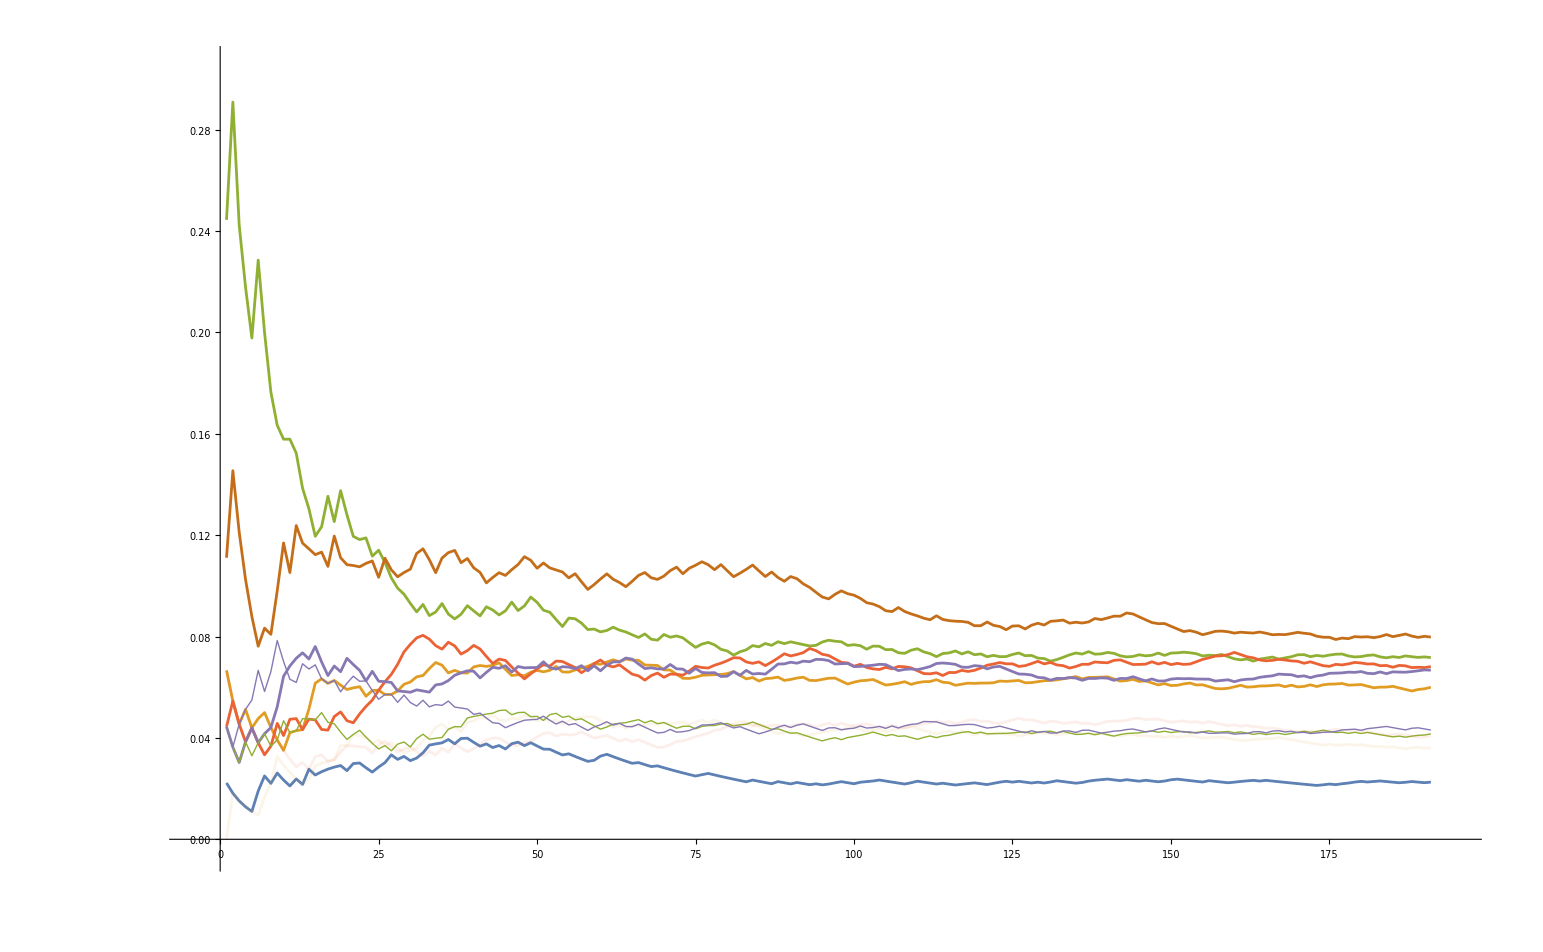

```mathematica
Show[G,Gwrong]
```